# Vaje 4

13. 3. 2025

## 1. kolokvij iz Matematike 1

1. Dokaži, da je za vsako naravno število  izraz  deljiv s .

```mathematica
ClearAll[izraz,izraz2]
izraz[n_] := 2^(2n+1)-9n^2+3n-2
izraz[0]
```

0

```mathematica
izraz[n+1]-izraz[n]//FullSimplify
```

6 (-1+4^n-3 n)

```mathematica
(*Deljivoz 6 torej tudi deljivo z 3*)
```

```mathematica
(*Ponovimo*)
izraz2[n_]:=-1+4^n-3 n
```

```mathematica
izraz2[n+1]-izraz2[n]//FullSimplify
```

3 (-1+4^n)

```mathematica
izraz3[n_]:=-1+4^n
```

```mathematica
izraz3[1]
```

3

```mathematica
izraz3[n+1]-izraz3[n]//FullSimplify
```

3 4^n

2.  Določi vsa realna števila , ki zadoščajo neenačbi .

```mathematica
Reduce[Abs[x^2+3x+2]+Abs[x+2]>2x^2+x]
```

-1<x<4

3. V kompleksnih številih reši enačbo . Rešitve nariši v kompleksni ravnini.

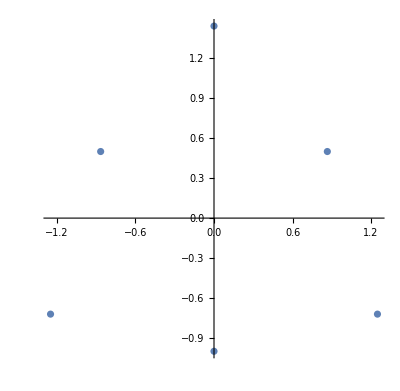

```mathematica
Solve[z^6+2I*z^3+3 == 0, {z}]//Values//Flatten//ComplexListPlot
```

4. Dana je množica . Ugotovi, katere od količin min A, inf A, max A in sup A obstajajo ter jih določi. Vse odgovore natančno utemelji.

```mathematica
a[n_]=(8n+2)/(4n-1)
Limit[a[x],x->Infinity]
```

(2+8 n)/(-1+4 n)

2

```mathematica
Reduce[{a[n+1] - a[n]<0, n>0, Element[n,Integers]},n] (*Padajoče*)
```

n∈ℤ&&n≥1

```mathematica
(*2 je infimum ne minimum*)
Solve[a[n] == 2,n]
```

{}

```mathematica
a[1]
```

10/3

```mathematica
(*Max = Sup = 10/3*)
```

```mathematica
Solve[{a[n]==0,n>0},n]
```

{}

## 2. kolokvij iz Matematike 1

1. Funkcija  je podana s predpisom

 
Izračunaj naravno definicijsko območje funkcije  in izračunaj kompozitum , kjer je 

g funkcija, ki je za  enaka , sicer pa je enaka .

```mathematica
f[x_]:=Log[ArcSin[Divide[3+x,3x-1]]]
```

```mathematica
g[x_]:=Piecewise[{
{E^x,x<=Log[Pi/2]},
{E^(-x),x>Log[Pi/2]}
}]
```

```mathematica
FunctionDomain[f[x],x]
```

x<-3||x≥2

```mathematica
g[f[x]]//FullSimplify
```

Piecewise[{{1/ArcSin[(3+x)/(-1+3 x)], Log[ArcSin[(3+x)/(-1+3 x)]]>Log[π/2]}, {ArcSin[(3+x)/(-1+3 x)], True}}]

2. Izračunaj naslednjo limito

.

```mathematica
Limit[Divide[n+2,Power[Factorial[n+1],1/n]],n->Infinity]
```

ⅇ

3. V odvisnosti od  preuči konvergenco zaporednja , ki je podano rekurzivno: , , kjer je  naravno število. V primerih ko zaporedje konvergira, zapiši še njegovo limito.

```mathematica
ClearAll[x,a]
```

```mathematica
a[1]:=x;
```

```mathematica
a[n_]:=Divide[(9-a[n-1])a[n-1],6];
f[x_]:=Divide[(9-x)x,6]
```

```mathematica
Solve[x==f[x],x]
```

{{x→0},{x→3}}

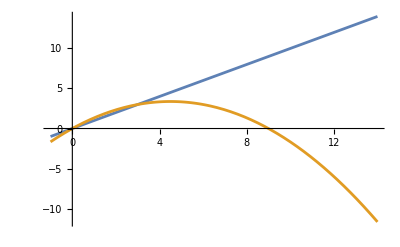

```mathematica
Plot[{x,f[x]},{x,-1,14}]
```

4. Poišči vsa realna števila , za katera konvergira vrsta 

.

```mathematica
ClearAll[a]
```

```mathematica
a[n_]:=Divide[x^n,x^(2n)+n]
```

```mathematica
kvocient =a[n+1]/a[n]//FullSimplify
```

(x (n+x^(2 n)))/(1+n+x^(2+2 n))

```mathematica
Reduce[{Limit[kvocient,n->Infinity]<1,Element[n,Integers],n>0},{x}]
```

n∈ℤ&&n≥1&&x>1

```mathematica
(*Za x>1 konvergira po kvoc. kriteriju *)
```

## 3. kolokvij iz Matematike 1

```mathematica
ClearAll[f,x,a]
```

```mathematica
f[x_]:=Piecewise[{
{ArcTan[Divide[1,x^2-1]],x>1},
{a,x==1},
{Divide[b*Sin[x-1],x^2-1],x<1}
}]
limita1 = Limit[f[x],x->1,Direction->"FromAbove"]
```

π/2

```mathematica
limita2 = a
```

a

```mathematica
limita3 = Limit[f[x],x->1,Direction->"FromBelow"]
```

b/2

```mathematica
Solve[limita1==limita2==limita3]
```

{{a→π/2,b→π}}

-Graphics-